```mathematica
WA = (a + b*z)*Exp[(-Sqrt[2])*z]
```

ⅇ^(-√2 z) (a+b z)

```mathematica
WAz = FullSimplify[D[WA, z]]
```

ⅇ^(-√2 z) (-√2 a+b-√2 b z)

```mathematica
WAzz = FullSimplify[D[WAz, z]]
```

2 ⅇ^(-√2 z) (a+b (-√2+z))

```mathematica
WAzzz = FullSimplify[D[WAzz, z]]
```

-2 ⅇ^(-√2 z) (√2 a+b (-3+√2 z))

```mathematica
WB = 1 + Exp[kp*z]*(c*Cos[km*z] + d*Sin[km*z])
```

1+ⅇ^(kp z) (c Cos[km z]+d Sin[km z])

```mathematica
WBz = FullSimplify[D[WB, z]]
```

ⅇ^(kp z) ((d km+c kp) Cos[km z]+(-c km+d kp) Sin[km z])

```mathematica
WBzz = FullSimplify[D[WBz, z]]
```

ⅇ^(kp z) ((2 d km kp+c (-km^2+kp^2)) Cos[km z]+(-2 c km kp+d (-km^2+kp^2)) Sin[km z])

```mathematica
WBzzz = FullSimplify[D[WBzz, z]]
```

ⅇ^(kp z) ((-d km^3-3 c km^2 kp+3 d km kp^2+c kp^3) Cos[km z]+(d kp (-3 km^2+kp^2)+c (km^3-3 km kp^2)) Sin[km z])

```mathematica
eqn1 = Simplify[WA-WB==0 /. z->0]
```

a==1+c

```mathematica
eqn2 = Simplify[WAz-WBz==0 /. z->0]
```

√2 a+d km+c kp==b

```mathematica
eqn3 = Simplify[WAzz-WBzz==0 /. z->0]
```

2 a+c km^2==2 √2 b+2 d km kp+c kp^2

```mathematica
eqn4 = Simplify[WAzzz-WBzzz==0 /. z->0]
```

2 √2 a+3 d km kp^2+c kp^3==6 b+d km^3+3 c km^2 kp

```mathematica
sol =FullSimplify[Solve[{eqn1,eqn2,eqn3,eqn4},{a,b,c,d}]]
```

{{a→((km^2+kp^2) (6+km^2+4 √2 kp+kp^2))/(4+km^4+2 km^2 (2+2 √2 kp+kp^2)+kp (8 √2+kp (12+4 √2 kp+kp^2))),b→(√2 (km^2+kp^2))/(2+km^2+2 √2 kp+kp^2),c→(2 (-2+km^2-4 √2 kp-3 kp^2))/(4+km^4+2 km^2 (2+2 √2 kp+kp^2)+kp (8 √2+kp (12+4 √2 kp+kp^2))),d→(-2 km^2 (4+5 √2 kp+3 kp^2)+2 kp (2 √2+kp (6+3 √2 kp+kp^2)))/(km (√2+kp) (4+km^4+2 km^2 (2+2 √2 kp+kp^2)+kp (8 √2+kp (12+4 √2 kp+kp^2))))}}

```mathematica
a = a/. sol[[1]][[1]]
```

((km^2+kp^2) (6+km^2+4 √2 kp+kp^2))/(4+km^4+2 km^2 (2+2 √2 kp+kp^2)+kp (8 √2+kp (12+4 √2 kp+kp^2)))

```mathematica
b = b /.sol[[1]][[2]]
```

(√2 (km^2+kp^2))/(2+km^2+2 √2 kp+kp^2)

```mathematica
c= c /.sol[[1]][[3]]
```

(2 (-2+km^2-4 √2 kp-3 kp^2))/(4+km^4+2 km^2 (2+2 √2 kp+kp^2)+kp (8 √2+kp (12+4 √2 kp+kp^2)))

```mathematica
d= d /.sol[[1]][[4]]
```

(-2 km^2 (4+5 √2 kp+3 kp^2)+2 kp (2 √2+kp (6+3 √2 kp+kp^2)))/(km (√2+kp) (4+km^4+2 km^2 (2+2 √2 kp+kp^2)+kp (8 √2+kp (12+4 √2 kp+kp^2))))

```mathematica
WB0 = Assuming[0<al<1,FullSimplify[WB /.{kp->(1/al^(1/2)+1)^(1/2),km->(1/al^(1/2)-1)^(1/2)}]]
```

(√(-1+1/al)+3 √2 √(-1+1/(√al))+8 √(1-al)+8 √2 √(√al-al)+5 √2 √(-1+1/(√al)) al+7 √((1-al) al)-ⅇ^(√(1+1/(√al)) z) ((√(1-al)+3 √2 √(√al-al)+5 √2 √(-1+1/(√al)) al+7 √(-(-1+al) al)) Cos[√(-1+1/(√al)) z]+(1-2 √al-(7+5 √2 √(1+1/(√al))) al+√2 √(√al+al)) Sin[√(-1+1/(√al)) z]))/((√2+√(1+1/(√al))) √(-1+1/(√al)) (1+√al) (1+3 √al+2 √2 √(√al+al)))

```mathematica
U0 = Assuming[0<al<1,FullSimplify[(1-(1-al)WB0)/al]]
```

1/al(1+((-1+√al) (√(-1+1/al)+3 √2 √(-1+1/(√al))+8 √(1-al)+8 √2 √(√al-al)+5 √2 √(-1+1/(√al)) al+7 √((1-al) al)-ⅇ^(√(1+1/(√al)) z) ((√(1-al)+3 √2 √(√al-al)+5 √2 √(-1+1/(√al)) al+7 √(-(-1+al) al)) Cos[√(-1+1/(√al)) z]+(1-2 √al-(7+5 √2 √(1+1/(√al))) al+√2 √(√al+al)) Sin[√(-1+1/(√al)) z])))/(√(-1+1/(√al)) (3 √2+√(1+1/(√al))+5 √2 √al+7 √(√al+al))))

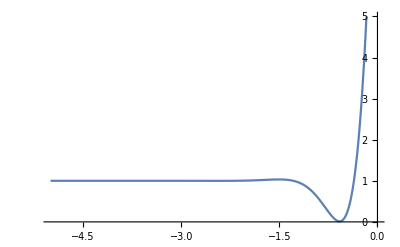

```mathematica
Plot[U0/. al->0.0064,{z,-5,0},PlotRange->{{-5,0},{0,5}}]
```

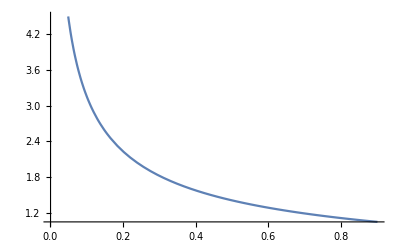

```mathematica
Plot[U0/. z->0,{al,0.001,0.9}]
```

```mathematica
U00 = Assuming[{0<al<1},FullSimplify[U0 /. z->0]]
```

(√(1-al)+3 √2 √(√al-al)+7 √((1-al) al)+5 √2 √((√al-al) al))/(√(-1+1/(√al)) al (3 √2+√(1+1/(√al))+5 √2 √al+7 √(√al+al)))